## Quantile Envelope (courtesy: Anton Antonov)

```mathematica
ClearAll[QuantileEnvelopeRegion];
QuantileEnvelopeRegion[points_?MatrixQ, quantile_?NumberQ, numberofDirections_?IntegerQ]:=Block[{nd = numberofDirections, dirs, rmats, qDirPoints,qRegion},
dirs = N@Flatten[
Table[{Cos[θ]Cos[ϕ], Sin[θ]Cos[ϕ],Sin[ϕ]},{θ, 2 π/(10 nd), 2 π,2 π/nd},
{ϕ,-π,π,2 π/nd}],1];
rmats = RotationMatrix[{{1,0,0},#}]&/@dirs;
qDirPoints =
Flatten[Map[Function[{m},Quantile[(m.Transpose[points])[[3]],quantile]], rmats]];
qRegion = ImplicitRegion[MapThread[(#1.{x,y,z})[[3]] ≤ #2 &, {rmats, qDirPoints}],{x,y,z}];
qRegion
]/;Dimensions[points][[2]] == 3 && 0 < quantile ≤ 1;
```

## extract cell masks and bounding boxes

```mathematica
fileSEG = "C:\\Users\\Ali Hashmi\\Desktop\\3D segmentation fixed spheroid\\C0.res";
Get[fileSEG];
```

```mathematica
primaryStats[seg_]:= Module[{areasM,avgcellsize,areaval},
areasM =ComponentMeasurements[seg,"Area"];
areaval = areasM[[All,2]];
Print[Style["total number of cells: ",{Bold,FontSize-> 14}], Style[Length@areasM,{Bold,FontSize-> 15}]];
Print[Style["average cell area in pixels: ",{Bold,FontSize-> 14}],Style[avgcellsize= Mean@areaval,{Bold,FontSize->15}]];
Print@SmoothHistogram[areaval/avgcellsize,PlotStyle->{Thick,XYZColor[0,0,1,0.8]},PlotLabel->"probable nuclei per blob"];
Print@ListPlot[areaval/avgcellsize,PlotStyle->{XYZColor[0,0,1,0.6],PointSize[Large]},PlotLabel->"probable nuclei per blob"];
Length@areasM
]
```

total number of cells: 412

average cell area in pixels: 16462.4

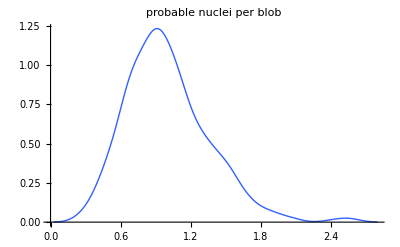

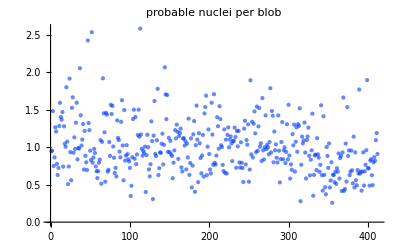

```mathematica
numcells=primaryStats[segM];
```

```mathematica
imageStackData[file_,roi_]:= Module[{bc,bc3d,img,imgData},
bc=Import@file;bc3d = Image3D[bc];
img = ImageTake[bc3d,Sequence@@roi];
Print@ImageAdjust[bc3d];
{ImageData[img],ImageDimensions[img]}
];
```

```mathematica
Clear@componentMeasures;
componentMeasures[file_]:= Module[{imgdata,roi,masksM,boxesM,iW,iD,iH},
roi=Thread[{1,Dimensions@segM}];
{imgdata,{iW,iD,iH}} = imageStackData[file,roi];
(* these represent the masks for and bounding box surrounding each cell *)
masksM = ComponentMeasurements[segM,"Mask"]; (* yields a sparse array with dimensions same as the imagestack *)
boxesM = ComponentMeasurements[segM,"BoundingBox"];
{masksM,boxesM,imgdata,iW,iD,iH}
];
```

```mathematica
file="C:\\Users\\Ali Hashmi\\Desktop\\3D segmentation fixed spheroid\\C0.tif";
```

```mathematica
{masksM,boxesM,imgdata,iW,iD,iH}=componentMeasures[file];
```

-Graphics3D-

## refined segmentation of a single cell

```mathematica
ClearAll@nucleiRefinement;
nucleiRefinement[id_,masksM_,boxesM_,imgdata_,iW_,iD_,iH_]:=With[{cellID = id},
Block[{b,c1,c2,c3,singlecellData,singlecellImage,singlecellImageBin,
pts,qRegion,qSurface,opts,gpts,outlierpts,singlecellImagefinal},
singlecellData=imgdata*masksM[[cellID,2]];
b = boxesM[[cellID,2]];
singlecellImage = ImageTake[Image3D@singlecellData,
{iH-b[[2,3]],iH-b[[1,3]]+1},{iD-b[[2,2]],iD-b[[1,2]]+1},{b[[1,1]],b[[2,1]]+1}];

(* here we develop a quantile envelope for the binarized cell imagedata *)
singlecellImageBin = Binarize@singlecellImage;
pts= ImageValuePositions[singlecellImageBin,1];
qRegion=QuantileEnvelopeRegion[pts,0.90,20];
qSurface = BoundaryDiscretizeRegion@qRegion;

c1=Max[pts[[All,1]]];
c2 = Max[pts[[All,2]]];
c3 = Max[pts[[All,2]]];

opts = {PlotRange-> {{0,c1+1},{0,c2+1},{0,c3}},Boxed-> True,Axes-> True,AxesLabel-> {"x","y","z"}};
gpts= Graphics3D@Point@pts;

(* make pixels outside the qsurface zero *)
outlierpts=Select[pts,x↦x∉qRegion];
singlecellImagefinal=ReplaceImageValue[singlecellImageBin,outlierpts-> 0];
GraphicsRow[{Show[qSurface,singlecellImage,Boxed-> True],
Show[{qSurface,gpts},opts],Show[singlecellImagefinal,qSurface]},ImageSize->Large]
]
];
```

```mathematica
nucleiRefinement[73,masksM,boxesM,imgdata,iW,iD,iH]
```

-Graphics-

## Refined segmentation of all nuclei in the spheroid

```mathematica
ClearAll@nucleiRefinement;
Options[nucleiRefinement]={quantile->0.90,directions->20};

Module[{imgdata=imgdata,masksM=masksM,boxesM=boxesM,iW=iW,iD=iD,iH=iH,numcells=numcells,segM=segM},

nucleiRefinement[seg_,id_,OptionsPattern[]]:=With[{cellID = id},
Block[{b,singlecellData,singlecellImage,singlecellImageBin,pts,qRegion,qSurface,outlierpts,inlyingpts,cellpos,segtemp,limits,unitcell},

Print["processing: ", cellID];
singlecellData=imgdata*masksM[[cellID,2]];
b = boxesM[[cellID,2]];
singlecellImage = ImageTake[Image3D@singlecellData,{iH-b[[2,3]],iH-b[[1,3]]+1},{iD-b[[2,2]],iD-b[[1,2]]+1},{b[[1,1]],b[[2,1]]+1}];

(* here we develop a quantile envelope for the binarized cell imagedata *)
singlecellImageBin = Binarize@singlecellImage;
pts= ImageValuePositions[singlecellImageBin,1];
qRegion=QuantileEnvelopeRegion[pts,OptionValue@quantile,OptionValue@directions];
qSurface = BoundaryDiscretizeRegion@qRegion;

(* make pixels outside qsurface zero *)
outlierpts=Select[pts,#∉qRegion&];
singlecellImageBin=ReplaceImageValue[singlecellImageBin,outlierpts-> 0];

(* now we need to replace the nucleus in the segmentation structure: zero whatever is initially present and then replace with inlyingpts *)
cellpos = Position[seg,cellID];
segtemp=ReplacePart[seg,cellpos-> 0];

(* lets pad the image to put cell in the right place *)
limits = {{b[[1,1]]-1,iW-b[[2,1]]-1},{b[[1,2]]-1,iD-b[[2,2]]-1},{b[[1,3]]-1,iH-b[[2,3]]}};
unitcell=MorphologicalComponents@ImagePad[singlecellImageBin,limits];
inlyingpts=Position[unitcell,1];

(* replace inlying pts with cell index *)
segtemp=ReplacePart[segtemp,inlyingpts-> cellID]
]
];

segNew=Fold[nucleiRefinement[#1,#2]&,segM,Range@numcells]

];
```

```mathematica
Colorize@segNew
```

-Graphics3D-

## Save the new segmentation structure

```mathematica
filesave = StringReplace[file,".tif"-> ".res2"];
Save[filesave,{segNew}]
```